```mathematica
x=Import["/tmp/attempt_count","Text"];
```

```mathematica
g=ImportString[#,"JSON"]&/@StringSplit[x,"\n"]
```

```mathematica
g={{"count"->6871,"mp_id"->1},{"count"->236947,"mp_id"->2},{"count"->153358,"mp_id"->3},{"count"->103954,"mp_id"->4},{"count"->128826,"mp_id"->5},{"count"->45328,"mp_id"->6},{"count"->10988,"mp_id"->10},{"count"->4925,"mp_id"->20},{"count"->6079,"mp_id"->30},{"count"->6358,"mp_id"->40},{"count"->17132,"mp_id"->50}};
```

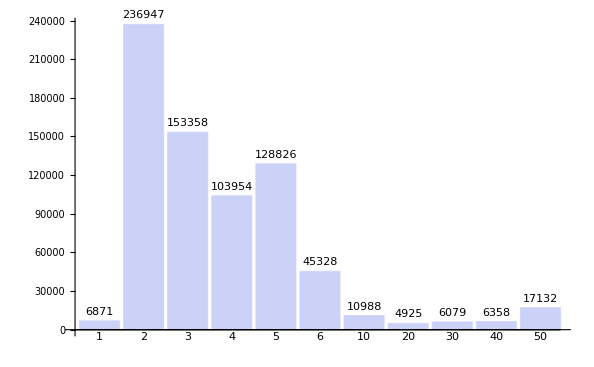

```mathematica
BarChart["count"/.g,ChartLabels->("mp_id"/.g),LabelingFunction->(Placed[Text[Style[#1,Medium]],Above]&)]
```

```mathematica
x=Import["/tmp/total_attempt_count","Text"];
```

```mathematica
g=ImportString[#,"JSON"]&/@StringSplit[x,"\n"]
```

```mathematica
g={{"count"->98352,"mp_id"->1},{"count"->1958663,"mp_id"->2},{"count"->1247664,"mp_id"->3},{"count"->829123,"mp_id"->4},{"count"->1127245,"mp_id"->5},{"count"->501104,"mp_id"->6},{"count"->91306,"mp_id"->10},{"count"->39194,"mp_id"->20},{"count"->46741,"mp_id"->30},{"count"->36477,"mp_id"->40},{"count"->131195,"mp_id"->50}};
```

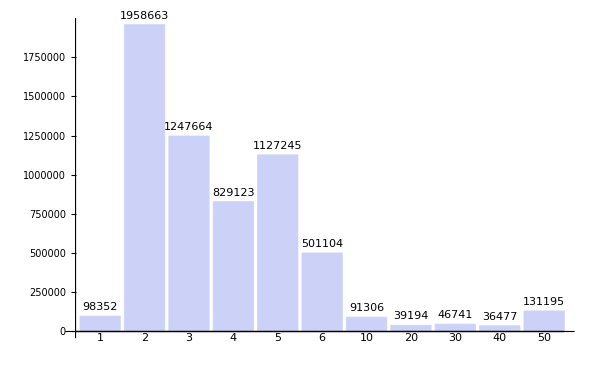

```mathematica
BarChart["count"/.g,ChartLabels->("mp_id"/.g),LabelingFunction->(Placed[Text[Style[#1,Medium]],Above]&)]
```

```mathematica
x=Import["/tmp/programTextSize","Text"];
```

```mathematica
g=ImportString["{"<>#,"JSON"]&/@StringSplit[x,"{"]
```

```mathematica
g={{"avgLength"->82.01208947635993,"count"->98350,"length"->8065889,"mp_id"->1},{"avgLength"->119.24209212822511,"count"->1958618,"length"->233549708,"mp_id"->2},{"avgLength"->142.39331990003575,"count"->1247646,"length"->177656456,"mp_id"->3},{"avgLength"->125.33954249075501,"count"->829098,"length"->103918764,"mp_id"->4},{"avgLength"->148.67992203801222,"count"->1127216,"length"->167594387,"mp_id"->5},{"avgLength"->193.07763659694547,"count"->501091,"length"->96749466,"mp_id"->6},{"avgLength"->83.15587246300616,"count"->91299,"length"->7592048,"mp_id"->10},{"avgLength"->115.84454253202021,"count"->39194,"length"->4540411,"mp_id"->20},{"avgLength"->136.5478528788754,"count"->46737,"length"->6381837,"mp_id"->30},{"avgLength"->128.74241925755334,"count"->36474,"length"->4695751,"mp_id"->40},{"avgLength"->159.264625399221,"count"->131193,"length"->20894404,"mp_id"->50}};
```

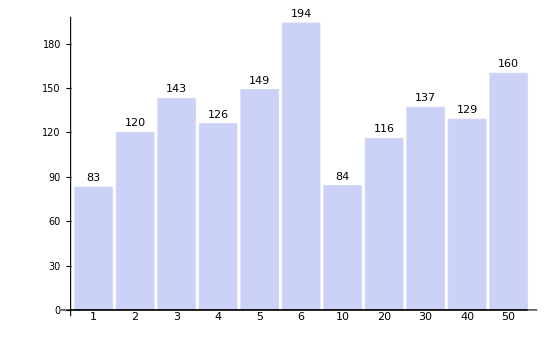

```mathematica
BarChart[Ceiling["avgLength"/.g],ChartLabels->("mp_id"/.g),LabelingFunction->(Placed[Text[Style[#1,Medium]],Above]&)]
```